```mathematica
(*          Computer Graphics with Applications of Dr. Makhanov. 
                               Lecture 3  
              2D and 3D functionality. Controls. Interpolation
*)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D}, ImageSize->Medium,AxesLabel->{"x","y","z"}];
```

```mathematica
(* We can use Mathematica to draw contour diagrams of functions of both two and three variables by using the functions ContourPlot and ContourPlot3D. In this lecture we will consider only ContourPlot. Let us start with something simple. 
This Example shows the contour lines of the function x^2+y^2 
We see a set of concentric circles with a coloring scheme that is dark in the center and becomes progressively lighter as we move out. Each circle is a contour or level set. The value of the function is constant along each contour. A really neat feature of ContourPlot is that Mathematica will display the value of the function at a specific contour if we move the mouse pointer to that contour *)
```

```mathematica
(* Contour plot and options  *)
```

```mathematica
fc[x_,y_]:=x^2+y^2
```

```mathematica
Plot3D[{fc[x,y],1,2},{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{0,8}}]
```

-Graphics3D-

```mathematica
(* Change some default for the ContourPlot *)
```

```mathematica
(* The BaseStyle-> controls the graphics font family size and color for a particular graph. In order to change the default options for every call of the ContourPlot use SetOptions[ ]. For instance *)
```

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Helvetica_Bold",Bold,FontSize->10,Black}];
```

```mathematica
(* Example (1) Check how the contour labels and the number of contours are controlled *)
```

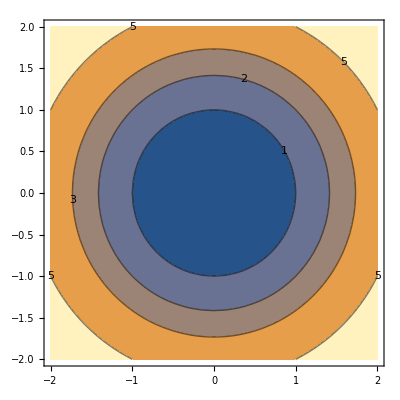

```mathematica
ContourPlot[fc[x,y],{x,-2,2},{y,-2,2},ContourLabels->True,Contours->{1,2,3,5}]
```

```mathematica
Options[ContourPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Helvetica_Bold,Bold,FontSize→10,GrayLevel[0]},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
(* Change some options. For example BaseStyle->{FontSize->18,Red}, ContourStyle->Dashed ColorFunction->"AplpineColors"}(this is a color scheme) *)
```

```mathematica
SetOptions[{ContourPlot},BaseStyle->{FontSize->14,Red},ContourStyle->Dashed,ColorFunction->"AlpineColors"];
```

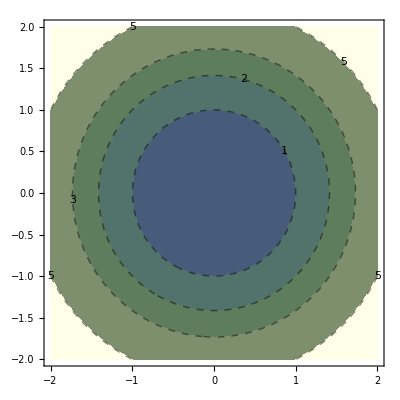

```mathematica
ContourPlot[fc[x,y],{x,-2,2},{y,-2,2},ContourLabels->True,Contours->{1,2,3,5}]
```

```mathematica
(* The specified options ColorFunction->"BeachColors" BaseStyle->Black override the default options, the contours are generated by a table TC3 *)
```

```mathematica
f2[x_,y_]:=Exp[-(x-Sin[ y])^2]
```

```mathematica
TC3=Table[0.1*i,{i,9}]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}

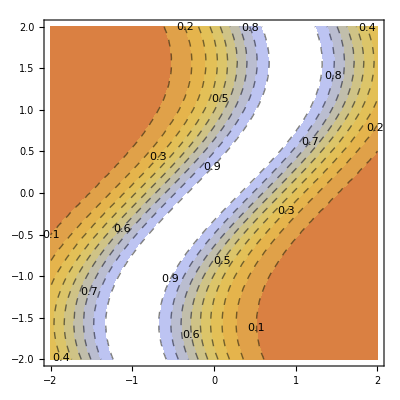

```mathematica
ContourPlot[f2[x,y],{x,-2,2},{y,-2,2},Contours->TC3,ContourLabels->True,BaseStyle->Black,ColorFunction->"BeachColors"]
```

```mathematica
(* Example (3) A number of is 5, the values are calculated automatically Contours->5  *)
```

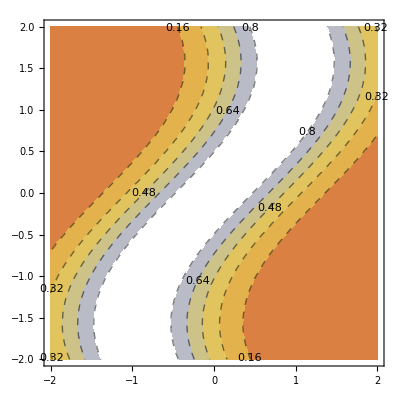

```mathematica
ContourPlot[f2[x,y],{x,-2,2},{y,-2,2},Contours->5,ContourLabels->True,BaseStyle->Black, ColorFunction->"BeachColors"]
```

```mathematica
(* Example (4) The next example uses ContourPlot3D to plot the contours of a function w=x y z. 
Although this function lives in a 4D space we can visualize it by plotting 3D intersections with the hyperplanes w=const. 
We use a couple of nice options to modify the plot. In particular,  we specify that the contours should correspond to functional values of w=−2,−1,0,1,and 2 and use ContourStyle to control the opacity of each contour surface.*)
```

```mathematica
f4[x_,y_,z_]:=x y z
```

```mathematica
TC4:={ -2,1,0,1,2} (* manual *)
```

```mathematica
ContourPlot3D[f4[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->TC4,ContourStyle ->Opacity[0.5]]
```

-Graphics3D-

```mathematica
(* Unlike ContourPlot ContourPlot3D does not display the value of the function as we move the mouse over the contours. Nor can we display those values with the ContourLabels which is no longer an allowable option. We are on our own here to understand what we are looking at! The line below shows how to plot a single contour f=1 using Contours->{0.1} *)
```

```mathematica
ContourPlot3D[f4[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{0.1},ContourStyle ->Opacity[0.8]]
```

-Graphics3D-

```mathematica
(* Let us change contour-surfaces using the Slider, from 0.3 to 0.5  *)
```

```mathematica
(* Slider "waiting" assignment  *)
```

```mathematica
MySlider4:={Slider[Dynamic[c],{0,3,0.5}],Dynamic[c]}
```

```mathematica
(* Graphic function  *)
```

```mathematica
plot4[c_]:=ContourPlot3D[f4[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{c},ContourStyle ->Opacity[ 0.8],ImageSize->Small]
```

```mathematica
(* Animation  *)
```

```mathematica
{MySlider4,Dynamic[plot4[c]]}
```

{{,},}

```mathematica
(* Toggler *)
```

```mathematica
(* Toggler dynamically updates the output from a given list when the output gets clicked *)
```

```mathematica
(* Example (5) TL defines a set of Toggler values *)
```

```mathematica
TL5={0.1,0.2,0.3,0.9} (*manual *)
```

{0.1,0.2,0.3,0.9}

```mathematica
Toggler[Dynamic[a],TL5,Background->Blue,BaseStyle->White]
```

```mathematica
Dynamic[a]
```

```mathematica
(* Let us change plot4[c] using the Toggler in the block {}; Define TL51 as a the set of Toggler values calculated using Table. They are 0.5, 1.5,....4.5  *)
```

```mathematica
TL51=Table[0.5i,{i,10}]
```

{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
MyToggler5:=Toggler[Dynamic[c],TL51,Background->Blue,BaseStyle->White]
```

```mathematica
{MyToggler5,Dynamic[plot4[c]]}
```

{,}

```mathematica
(* Example (5') switch the Opacity of ContourPlot3D[f4[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{1},ContourStyle ->Opacity[op],Mesh-> False]
as op={0.1,0.2,0.3,0.4.0.5,0.75,0.9,1.0} using Toggler *)
```

```mathematica
plot5[op_]:=ContourPlot3D[f4[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->{1},ContourStyle ->Opacity[op],Mesh-> False,ImageSize->Small]
```

```mathematica
TOp={0.1,0.2,0.3,0.5,0.75,0.9,1.0}
```

{0.1,0.2,0.3,0.5,0.75,0.9,1.}

```mathematica
MyToggler51:=Toggler[Dynamic[op],TOp,Background->Blue,BaseStyle->White]
```

```mathematica
{MyToggler51,Dynamic[plot5[op]]}
```

{,}

```mathematica
(* Example (5'') Setup a Toggler to change the number of contours as follows c1={2,4,6,8,10,12,14}*)
```

```mathematica
TN5= Table[2i,{i,1,7}](* Table *)
```

{2,4,6,8,10,12,14}

```mathematica
MyToggler52:=Toggler[Dynamic[c1],TN5,Background->Pink,BaseStyle->Black]
```

```mathematica
plot51[c1_]:=ContourPlot3D[f4[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->c1,ContourStyle ->Opacity[0.8]]
```

```mathematica
{Dynamic[plot51[c1]],MyToggler52}
```

{,}

```mathematica
(* Radio button Bar for plot51[c1] *)
```

```mathematica
MyRBar52:=RadioButtonBar[Dynamic[c1],TN5,Background->Purple]
```

```mathematica
{Dynamic[plot51[c1]],MyRBar52}
```

{, | 2   | 4   | 6   | 8   | 10   | 12   | 14}

```mathematica
(* Example (6) Animate Sin[k1*x*y]*Exp[k2*(x^2-y^2)] where k1 is a Toggler {1,5,7,10,-3} and k2 is a Slider changing from 0 to 5 with step 0.1
Fix the PlotRange (in class)  *)
```

```mathematica
f6[x_,y_,k1_,k2_]:=Sin[k1*x*y]*Exp[k2*(x^2-y^2)]
```

```mathematica
MyToggler6:=Toggler[Dynamic[k1],{1,5,7,10,-3},Background->Blue,BaseStyle->White]
```

```mathematica
MySlider6:={Slider[Dynamic[k2],{0,5,0.1},Background->Blue], Dynamic[k2]}
```

```mathematica
plot6[k1_,k2_]:=Plot3D[f6[x,y,k1,k2],{x,-1,1},{y,-1,1},Mesh->True,PlotRange->2]
```

```mathematica
{Dynamic[plot6[k1,k2]],MySlider6,MyToggler6}
```

{,{,},}

```mathematica
(* Example (7) PopupMenu[x,{val1,...valn}] takes the setting to be the dynamically updated current value of x  with the value of x  being reset every time an item is selected from the menu *)
```

```mathematica
PopupMenu[Dynamic[xxx],{1,2,3}]
```

```mathematica
Dynamic[xxx]
```

```mathematica
PopupMenu[Dynamic[xx],{1->"0ne",2->"Two",3->"anything"}]
```

```mathematica
Dynamic[xx]
```

```mathematica
(*Consider graph of f6 for k1=2 and k2=3 with the color updated from the PopupMenu*)
```

```mathematica
MyPopMenu7:=PopupMenu[Dynamic[color1],{Red,Green ,Blue,Purple,Pink,LightBlue}]
```

```mathematica
{Dynamic[Plot3D[f6[x,y,2,3],{x,-1,1},{y,-1,1}, PlotStyle->color1] ],MyPopMenu7}
```

{,}

```mathematica
(* A menu with textual items is shown below *)
```

```mathematica
MyPopMenu71:=PopupMenu[Dynamic[color2],{Red->"Red",Green->"Green" ,Blue->"Blue",Purple->"Purple",Pink->"Pink"}]
```

```mathematica
plot66[color2_]:=Plot3D[f6[x,y,2,3],{x,-1,1},{y,-1,1}, PlotStyle->color2]
```

```mathematica
{Dynamic[plot66[color2]],MyPopMenu71}
```

{,}

```mathematica
(* Interpolation *)
```

```mathematica
(* Interpolation[data] performs spline interpolation. The data is defined using the structures defined below *)
```

```mathematica
(* Example 15 *)
```

```mathematica
(* data1 defines the y-values, x values are integers 1,2,... *)
```

```mathematica
data1:={1,2,5,7,8,-5,6,-3}
```

```mathematica
(* Plot the points *)
```

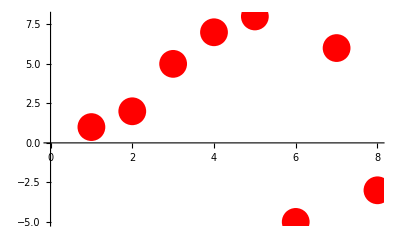

```mathematica
plot15points=ListPlot[data1,PlotStyle->{PointSize[0.05],Red}]
```

```mathematica
(* f15 interpolating functions*)
```

```mathematica
f15=Interpolation[data1,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
data1
```

{1,2,5,7,8,-5,6,-3}

```mathematica
(* check f15 vs. the data *)
```

```mathematica
Table[f15[i],{i,Length[data1]}]
```

{1.,2.,5.,7.,8.,-5.,6.,-3.}

```mathematica
(* Plot *)
```

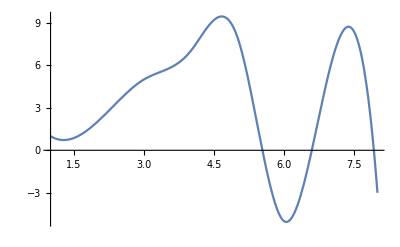

```mathematica
plot151=Plot[f15[x],{x,1,Length[data1]}]
```

```mathematica
(* Superimpose *)
```

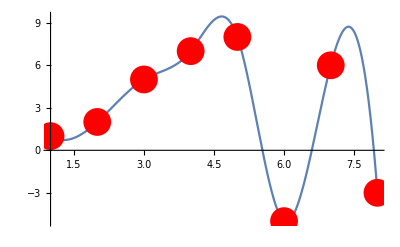

```mathematica
Show[plot151,plot15points]
```

```mathematica
(* Example (16) Interpolate an (x,y) data  *)
```

```mathematica
data2={{1,1},{2,3},{-1,-3},{7,0},{4,-4}} (* (x1,y1),(x2,y2),(x3,y3)..... *)
```

{{1,1},{2,3},{-1,-3},{7,0},{4,-4}}

```mathematica
f16=Interpolation[data2,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
minx=Min[Transpose[data2][[1]]]
```

-1

```mathematica
maxx=Max[Transpose[data2][[1]]]
```

7

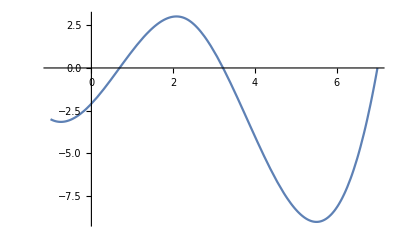

```mathematica
plot161=Plot[f16[x],{x,minx,maxx}]
```

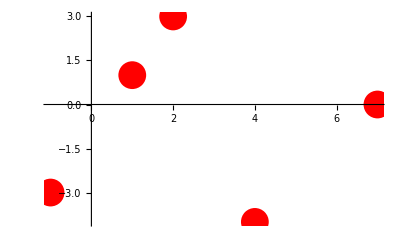

```mathematica
plot162=ListPlot[data2,PlotStyle->{PointSize[0.05],Red}]
```

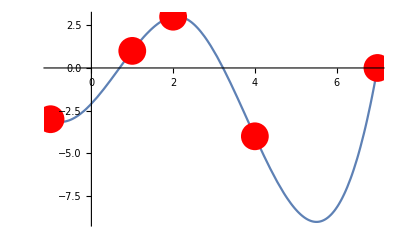

```mathematica
Show[plot161,plot162]
```

```mathematica
(* Example (17) Alternatively (and this is a much better choice) you can sort the data and generate a parametric function  as follows *)
```

```mathematica
MatrixForm[data2]
```

(1 | 1
2 | 3
-1 | -3
7 | 0
4 | -4)

```mathematica
x2=Transpose[data2][[1]]  (* extracts x *)
```

{1,2,-1,7,4}

```mathematica
y2=Transpose[data2][[2]](* extracts y *)
```

{1,3,-3,0,-4}

```mathematica
Ordered=Ordering[x2]
```

{3,1,2,5,4}

```mathematica
x22=x2[[Ordered]]
```

{-1,1,2,4,7}

```mathematica
y22=y2[[Ordered]]
```

{-3,1,3,-4,0}

```mathematica
sx17:=Interpolation[x22,Method->"Spline"] (* t={1,2,3,4} *)
```

```mathematica
sy17:=Interpolation[y22,Method->"Spline"]
```

```mathematica
spline17[t_]={sx17[t],sy17[t]} (* parametric function *)
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

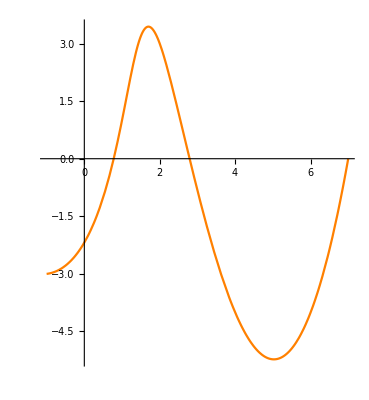

```mathematica
plot17=ParametricPlot[spline17[t],{t,1,Length[x22]},PlotStyle->Orange]
```

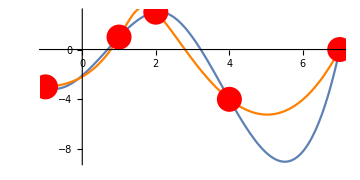

```mathematica
Show[{plot161,plot17,plot162}, AspectRatio->0.5,ImageSize->Medium]
```

```mathematica
(* Example (18) The above works applies to interpolation of space curves. Let us construct 3D splines passing through points defined by a list data3 *)
```

```mathematica
data3:={{2,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
```

```mathematica
MatrixForm[data3]
```

(2 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
x3=Transpose[data3][[1]]
```

{2,4,2,1,2,4}

```mathematica
y3=Transpose[data3][[2]]
```

{2,5,5,1,-6,4}

```mathematica
z3=Transpose[data3][[3]]
```

{4,-1,0,3,-6,4}

```mathematica
data3:={{2,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
```

```mathematica
MatrixForm[data3]
```

(2 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
sx19=Interpolation[x3,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
sy19=Interpolation[y3,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
sz19=Interpolation[z3,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
s19[t_]:={sx19[t],sy19[t],sz19[t]} (* 3D parametric function (vector-function)  *)
```

```mathematica
plot191=ParametricPlot3D[s19[t],{t,1,Length[x3]},PlotStyle->{Red, Thickness[0.02]},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
plot192=ListPointPlot3D[data3,PlotStyle->{PointSize[0.07],Blue},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Show[{plot191,plot192}]
```

-Graphics3D-

```mathematica
(*  Example (19) interpolation of surfaces *)
```

```mathematica
(* Interpolate a 3D data given by the heights of the explicit function z=f(x,y) as follows
{{2,3,4,1},
{2,-1,6,1},
{1,0,0,1},
{1,0,0,-1}}
 *)
```

```mathematica
data41={
{2,3,4,1},
{2,-1,6,1},
{1,0,0,1},
{1,0,0,-1},
{1,3,3,5}}
```

{{2,3,4,1},{2,-1,6,1},{1,0,0,1},{1,0,0,-1},{1,3,3,5}}

```mathematica
MatrixForm[data41] (* x=1,2,3,4-column number  y==1,2,3,4,5 row number} *)
```

(2 | 3 | 4 | 1
2 | -1 | 6 | 1
1 | 0 | 0 | 1
1 | 0 | 0 | -1
1 | 3 | 3 | 5)

```mathematica
PL1=ListPointPlot3D[data41,PlotStyle->PointSize[0.05],BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
MatrixForm[data41]
```

(2 | 3 | 4 | 1
2 | -1 | 6 | 1
1 | 0 | 0 | 1
1 | 0 | 0 | -1
1 | 3 | 3 | 5)

```mathematica
Tdata41=Transpose[data41]
```

{{2,2,1,1,1},{3,-1,0,0,3},{4,6,0,0,3},{1,1,1,-1,5}}

```mathematica
(* We need to transpose the matrix to comply with the way the ListInterpolation interpolates the data ]*)
```

```mathematica
MatrixForm[Tdata41]
```

(2 | 2 | 1 | 1 | 1
3 | -1 | 0 | 0 | 3
4 | 6 | 0 | 0 | 3
1 | 1 | 1 | -1 | 5)

```mathematica
f21:=ListInterpolation[Tdata41]
```

```mathematica
(* Date range *)
```

```mathematica
DRange=Dimensions[Tdata41]
```

{4,5}

```mathematica
(* x-range *)
```

```mathematica
xL=DRange[[1]]
```

4

```mathematica
(* y-range *)
```

```mathematica
yL=DRange[[2]]
```

5

```mathematica
(* Check the output against Tdata41 *)
```

```mathematica
MatrixForm[Tdata41]
```

(2 | 2 | 1 | 1 | 1
3 | -1 | 0 | 0 | 3
4 | 6 | 0 | 0 | 3
1 | 1 | 1 | -1 | 5)

```mathematica
f21[3,2]
```

6

```mathematica
(* Plot the surface *)
```

```mathematica
PL2=Plot3D[f21[x,y],{x,1,xL},{y,1,yL},PlotStyle->Opacity[0.7]]
```

-Graphics3D-

```mathematica
(* Superimpose  *)
```

```mathematica
Show[{PL1,PL2},Boxed->True] (* beautify it *)
```

-Graphics3D-

```mathematica
(* Self/Study  This combines the two subjects presented in this lecture i.e. the control structures and interpolation *)
```

```mathematica
(* Interpolate selecting interactively from 3 different sets of data *)
```

```mathematica
Data1={1,5,6,8,9,-8,-7,-1,0,0,0}
```

{1,5,6,8,9,-8,-7,-1,0,0,0}

```mathematica
Data2={0,0,16,18,-3,-8,-7}
```

{0,0,16,18,-3,-8,-7}

```mathematica
Data3={1,7,6,8,0,7,9,2,1,-1,-11,-12,-7,-3,2,0,0,0}
```

{1,7,6,8,0,7,9,2,1,-1,-11,-12,-7,-3,2,0,0,0}

```mathematica
DataAll={Data1,Data2,Data3}
```

{{1,5,6,8,9,-8,-7,-1,0,0,0},{0,0,16,18,-3,-8,-7},{1,7,6,8,0,7,9,2,1,-1,-11,-12,-7,-3,2,0,0,0}}

```mathematica
fi[data_]:=Interpolation[data,Method->"Spline"]
```

```mathematica
MyDataMenu71:=PopupMenu[Dynamic[index],{1->"Data1",2->"Data2" ,3->"Data3"}]
```

```mathematica
MyListPlot[index_]:=ListPlot[DataAll[[index]],PlotStyle->{PointSize[0.03],Red}]
```

```mathematica
MyPlot[fdata_,index_]:=Plot[fdata[x],{x,1,Length[DataAll[[index]]]}]
```

```mathematica
ShowPlots[fdata_,index_]:=Show[MyPlot[fdata,index],MyListPlot[index]]
```

```mathematica
(* Check *)
```

```mathematica
MyDataMenu71
```

```mathematica
Dynamic[fcheck=fi[DataAll[[index]]]]
```

```mathematica
Dynamic[MyPlot[fcheck,index]]
```

```mathematica
Dynamic[MyListPlot[index]]
```

```mathematica
(* Final code *)
```

```mathematica
{Dynamic[fdata=Interpolation[DataAll[[index]],Method->"Spline"]],Dynamic[ShowPlots[fdata,index]],MyDataMenu71}
```

{,,}